```mathematica
<<IFEM`
```

```mathematica
NeoHookeanPotential[F_,λ_,μ_]:=(
μ /2(Tr[Fᵀ.F]-2)-μ Log[Det[F]]+λ/2 Log[Det[F]]^2
)
NeoHookeanPotential[σx_,σy_,λ_,μ_]:=1/2 (μ (-2+σx^2+σy^2)-2 μ Log[σx σy]+λ Log[σx σy]^2)
NeoHookeanStress[F_,λ_,μ_]:=(
μ(F-Inverse[F]ᵀ)+λ Log[Det[F]] Inverse[F]ᵀ
)
NeoHookeanStressDifferential[F_,dF_,λ_,μ_]:=(
μ dF+(μ-λ Log[Det[F]])Inverse[F]ᵀ.dFᵀ.Inverse[F]ᵀ+λ Tr[Inverse[F]ᵀ.dFᵀ] Inverse[F]ᵀ
)
```

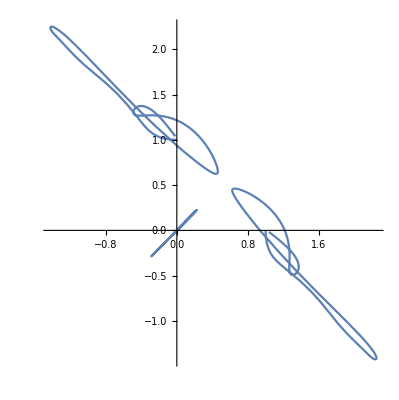

```mathematica
vA={{0,0},{0,1},{1,0}};
vInit = vA+0.7{{0,1},{0,0},{0,0}};
dv = {{-.05,.1},{-.2,.3},{.4,.5}};
t1=10;
fExt[t_]={{1,1},{-1,0},{0,-1}}HeavisideTheta[3-t];
vertices[t_]=ElasticTriangleSimulation[
vA, fExt,
NeoHookeanStress[#,1,1]&,
NeoHookeanStressDifferential[#1,#2,1,1]&,t1,
.1];
ParametricPlot[vertices[t],{t,0,t1}]
Animate[
Graphics[Triangle[vertices[t]],Axes->True,PlotRange->{{-2,2},{-2,2}}]
,{t,0,t1}
]
```

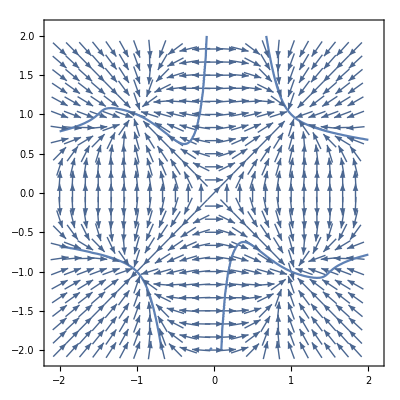

```mathematica
(* primary contour visualization *)
FSVD = ({{Cos[ϕ], -Sin[ϕ]}, {Sin[ϕ], Cos[ϕ]}}).({{sx, 0}, {0, sy}}).({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}});
ψv[sx_,sy_]=FullSimplify[NeoHookeanPotential[FSVD,λ,μ]];
vf=-D[ψv[sx,sy],{{sx,sy}}]/.{μ->1,λ->1};
vp=VectorPlot[Re[vf],{sx,-2,2},{sy,-2,2},VectorScale->{Automatic,Automatic,None},VectorStyle->Tiny,
VectorPoints->Fine];
grad=D[ψv[sx,sy],{{sx, sy}}];
Hess=FullSimplify[D[grad,{{sx,sy}}]];
temp=FullSimplify[Eigensystem[Hess]];
Simplify[temp[[1,1]]-temp[[1,2]]];
eigenv=temp[[2,2]];
cont = Re[(grad.eigenv)]/.{μ->1,λ->1};
Show[{vp,ContourPlot[cont==0,{sx,-2,2},{sy,-2,2}]}]
```